## Prior on localization n1, n2

### Inverse - gamma distribution

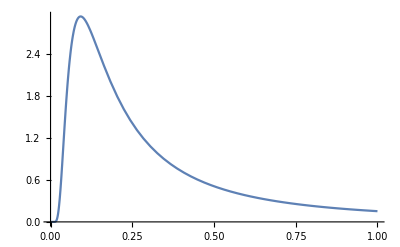

{6.25788×10^-6,6.25788×10^-6}

```mathematica
interval = {0.01, 100};
(*nScale = 1;*)
α=1;
(*β=nScale * (α+1);*)
β=0.18422522996251992;
mode = β/(α+1);


p[n_]:=β^α/Gamma[α] n^(-α-1)Exp[-β/n];
Plot[p[n],{n,0, 1}, PlotRange->All]
(p/@interval)/p[mode]
(*LogLinearPlot[p[n], {n, 10^-6, 10^3}, PlotRange->All]
Plot[p[n], {n, 0, 0.5}, PlotRange->All]*)
```

## Diffusivity prior

Inverse - Gamma distribution. D0 through the mean

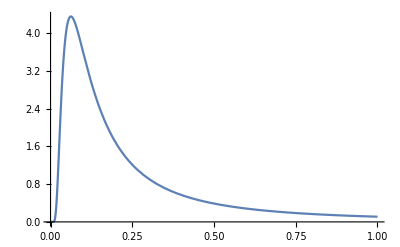

895.13

{0.00487756,0.00485753}

```mathematica
interval = {0.01, 5};
DScale = 0.5;
α=1; 
(*β=DScale * (α+1);*)
β=0.1245;
mode = β/(α+1);
(*τ =1/100;
Clear[β];*)
 dPrior[d_]:=β^α/Gamma[α] d^(-α-1)Exp[-β/d];
(*sol =FindRoot[dPrior[5]/ dPrior[β/(α+1)]==τ,{β,10^-7,1}]*)
Plot[dPrior[d]/.sol,{d,0, 1}, PlotRange->All]
dPrior[β/(α+1)]/dPrior[5]
(dPrior/@interval)
```

## Link strength

### Gamma distribution for link strength

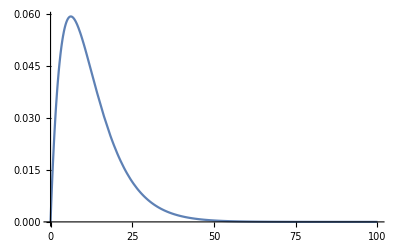

{4.38135×10^-6,4.38135×10^-6}

```mathematica
interval = {10^-5,100};
(*τ = 1/100;*)
(*nScale = 1;*)
k=2;
(*θ=nScale/(k-1);*)
θ=6.20420626391148;
mode = (k-1) * θ;
(*M = mode = (k-1) *)
(*Clear[α]
αRoot = FindRoot[{Exp[-1+α]-α/τ},{α,10}]
θ=interval[[2]]/α/.αRoot
*)
prior[n12_]:=1/(Gamma[k] θ^k)n12^(k-1)Exp[-n12/θ];
Plot[prior[n12],{n12,0, 100}, PlotRange->All]
(prior/@interval)/prior[mode]
(*Print["Var=", α/(α-1) θ^2]*)
```